```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/yannick/janr_bosted_2016

### Number of bootstrap-datasets:

```mathematica
NBoot=125
```

125

### Values of Q^2 corresponding to original [Inna,(2009)]-bins:

```mathematica
Q2Values={0.3,0.4,0.5,0.65,0.9,1.72,2.05,2.44,2.91,3.48,4.16}
```

{0.3,0.4,0.5,0.65,0.9,1.72,2.05,2.44,2.91,3.48,4.16}

```mathematica
Q2ValDeltaI={0.3,0.4,0.525,0.65,0.75,0.9,1.15,1.45,3.0,3.5,4.2,5.0,6.0}
```

{0.3,0.4,0.525,0.65,0.75,0.9,1.15,1.45,3.,3.5,4.2,5.,6.}

```mathematica
Q2ValDeltaII={0.16,0.2,0.24,0.28,0.3,0.32,0.36,0.4,0.525,0.65,0.75,0.9,1.15,1.45,3.0,3.5,4.2,5.0,6.0}
```

{0.16,0.2,0.24,0.28,0.3,0.32,0.36,0.4,0.525,0.65,0.75,0.9,1.15,1.45,3.,3.5,4.2,5.,6.}

### Read-in the multipole-parameters (ImM_(1+),R_EM,R_SM), with statistical and systematic errors, for the Δ(1232)-resonance:

```mathematica
ImM={5.122,4.803,4.238,3.794,3.356,2.962,2.438,1.880,0.693,0.558,0.412,0.312,0.191}
```

{5.122,4.803,4.238,3.794,3.356,2.962,2.438,1.88,0.693,0.558,0.412,0.312,0.191}

```mathematica
StatImM={0.130,0.122,0.109,0.097,0.088,0.078,0.066,0.059,0.022,0.018,0.014,0.012,0.012}
```

{0.13,0.122,0.109,0.097,0.088,0.078,0.066,0.059,0.022,0.018,0.014,0.012,0.012}

```mathematica
SysImM={0.004,0.005,0.008,0.009,0.011,0.012,0.013,0.014,0.016,0.017,0.018,0.023,0.027}
```

{0.004,0.005,0.008,0.009,0.011,0.012,0.013,0.014,0.016,0.017,0.018,0.023,0.027}

```mathematica
REM={-1.7,-1.6,-2.1,-1.6,-2.1,-1.6,-1.5,-2.4,-2.0,-1.4,-1.9,-2.1,-2.6,-2.5,-2.3,-1.1,-2.9,-3.2,-3.6}/100.
```

{-0.017,-0.016,-0.021,-0.016,-0.021,-0.016,-0.015,-0.024,-0.02,-0.014,-0.019,-0.021,-0.026,-0.025,-0.023,-0.011,-0.029,-0.032,-0.036}

```mathematica
StatREM={0.1,0.2,0.2,0.2,0.2,0.2,0.3,0.2,0.3,0.3,0.4,0.5,0.5,0.7,0.4,0.5,0.7,1.5,2.6}/100.
```

{0.001,0.002,0.002,0.002,0.002,0.002,0.003,0.002,0.003,0.003,0.004,0.005,0.005,0.007,0.004,0.005,0.007,0.015,0.026}

```mathematica
SysREM={0.04,0.04,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.2,0.2,0.2,0.2,0.3,0.4,0.4,1.5}/100.
```

{0.0004,0.0004,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.002,0.002,0.002,0.002,0.003,0.004,0.004,0.015}

```mathematica
RSM={-4.6,-4.4,-4.5,-5.4,-5.0,-5.5,-5.2,-5.2,-5.5,-6.2,-6.7,-8.1,-8.0,-9.6,-11.4,-12.4,-15.9,-25.2,-25.3}/100.
```

{-0.046,-0.044,-0.045,-0.054,-0.05,-0.055,-0.052,-0.052,-0.055,-0.062,-0.067,-0.081,-0.08,-0.096,-0.114,-0.124,-0.159,-0.252,-0.253}

```mathematica
StatRSM={0.2,0.2,0.3,0.3,0.2,0.3,0.3,0.2,0.3,0.4,0.4,0.4,0.5,0.8,0.6,0.8,1.3,2.7,5.3}/100.
```

{0.002,0.002,0.003,0.003,0.002,0.003,0.003,0.002,0.003,0.004,0.004,0.004,0.005,0.008,0.006,0.008,0.013,0.027,0.053}

```mathematica
SysRSM={0.04,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.2,0.2,0.2,0.2,0.2,0.2,0.4,0.7,1.5,3.8}/100.
```

{0.0004,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.002,0.002,0.002,0.002,0.002,0.002,0.004,0.007,0.015,0.038}

### Read-in the electrocouplings, with statistical and systematic errors, for resonances N(1440), N(1520) and N(1535):

```mathematica
N1440A12={-24.0,-19.7,-4.6,5.4,18.7,58.5,62.9,56.2,42.5,32.6,23.1}
```

{-24.,-19.7,-4.6,5.4,18.7,58.5,62.9,56.2,42.5,32.6,23.1}

```mathematica
StatN1440A12={1.2,1.1,1.3,1.2,2.7,1.1,0.9,0.9,1.1,0.9,2.2}
```

{1.2,1.1,1.3,1.2,2.7,1.1,0.9,0.9,1.1,0.9,2.2}

```mathematica
SysN1440A12={2.5,3.1,3.4,3.4,4.3,4.3,3.4,3.4,3.0,2.8,4.9}
```

{2.5,3.1,3.4,3.4,4.3,4.3,3.4,3.4,3.,2.8,4.9}

```mathematica
N1440S12={37.6,34.8,36.9,35.2,36.2,26.9,15.5,11.8,13.8,14.1,17.5}
```

{37.6,34.8,36.9,35.2,36.2,26.9,15.5,11.8,13.8,14.1,17.5}

```mathematica
StatN1440S12={1.9,1.3,1.6,1.2,2.1,1.3,1.5,1.4,2.1,2.4,2.6}
```

{1.9,1.3,1.6,1.2,2.1,1.3,1.5,1.4,2.1,2.4,2.6}

```mathematica
SysN1440S12={2.5,3.0,3.0,3.4,4.2,5.4,5.0,4.3,2.6,2.4,5.6}
```

{2.5,3.,3.,3.4,4.2,5.4,5.,4.3,2.6,2.4,5.6}

```mathematica
N1535A12={90.9,92.9,91.7,91.6,85.5,75.7,65.4,59.8,53.0,41.0,31.8}
```

{90.9,92.9,91.7,91.6,85.5,75.7,65.4,59.8,53.,41.,31.8}

```mathematica
StatN1535A12={2.3,1.6,2.0,1.8,2.3,1.4,1.7,2.2,1.9,2.4,3.6}
```

{2.3,1.6,2.,1.8,2.3,1.4,1.7,2.2,1.9,2.4,3.6}

```mathematica
SysN1535A12={1.8,2.2,2.7,3.3,5.2,4.9,4.0,3.9,4.5,4.6,4.5}
```

{1.8,2.2,2.7,3.3,5.2,4.9,4.,3.9,4.5,4.6,4.5}

```mathematica
N1535S12={-13.0,-15.9,-16.7,-14.4,-16.4,-24.8,-19.9,-16.7,-12.6,-11.3,-8.9}
```

{-13.,-15.9,-16.7,-14.4,-16.4,-24.8,-19.9,-16.7,-12.6,-11.3,-8.9}

```mathematica
StatN1535S12={2.2,2.0,2.4,1.9,3.9,1.6,1.9,2.9,2.8,3.4,5.9}
```

{2.2,2.,2.4,1.9,3.9,1.6,1.9,2.9,2.8,3.4,5.9}

```mathematica
SysN1535S12={2.1,2.2,2.4,2.3,4.9,3.3,4.4,4.3,4.2,2.8,3.8}
```

{2.1,2.2,2.4,2.3,4.9,3.3,4.4,4.3,4.2,2.8,3.8}

```mathematica
N1520A12={-54.1,-59.7,-60.6,-64.5,-64.9,-38.8,-39.7,-36.3,-31.0,-24.9,-20.9}
```

{-54.1,-59.7,-60.6,-64.5,-64.9,-38.8,-39.7,-36.3,-31.,-24.9,-20.9}

```mathematica
StatN1520A12={1.8,2.1,2.2,1.8,2.2,1.3,1.5,1.4,1.9,2.2,4.2}
```

{1.8,2.1,2.2,1.8,2.2,1.3,1.5,1.4,1.9,2.2,4.2}

```mathematica
SysN1520A12={1.8,2.4,2.5,2.7,2.9,3.9,3.2,2.6,2.2,2.9,3.2}
```

{1.8,2.4,2.5,2.7,2.9,3.9,3.2,2.6,2.2,2.9,3.2}

```mathematica
N1520A32={75.1,67.6,60.0,54.2,44.1,21.4,18.3,13.4,9.6,8.2,4.6}
```

{75.1,67.6,60.,54.2,44.1,21.4,18.3,13.4,9.6,8.2,4.6}

```mathematica
StatN1520A32={2.2,1.9,1.9,1.6,2.6,1.2,1.6,1.7,2.0,2.2,3.2}
```

{2.2,1.9,1.9,1.6,2.6,1.2,1.6,1.7,2.,2.2,3.2}

```mathematica
SysN1520A32={2.1,2.2,2.4,2.8,3.1,3.5,2.6,1.9,2.7,5.2,6.9}
```

{2.1,2.2,2.4,2.8,3.1,3.5,2.6,1.9,2.7,5.2,6.9}

```mathematica
N1520S12={-48.4,-43.6,-39.4,-37.5,-34.3,-9.1,-6.8,-3.6,-2.3,-2.6,-0.7}
```

{-48.4,-43.6,-39.4,-37.5,-34.3,-9.1,-6.8,-3.6,-2.3,-2.6,-0.7}

```mathematica
StatN1520S12={2.4,2.1,2.4,1.9,3.1,1.0,1.5,1.9,2.1,2.6,4.6}
```

{2.4,2.1,2.4,1.9,3.1,1.,1.5,1.9,2.1,2.6,4.6}

```mathematica
SysN1520S12={2.3,2.4,2.8,2.5,3.0,1.8,1.9,1.6,1.6,2.4,3.2}
```

{2.3,2.4,2.8,2.5,3.,1.8,1.9,1.6,1.6,2.4,3.2}

### Perform the bootstrap - preparation for the Δ-resonance:

```mathematica
BootPrepImM=Table[{ImM[[i]],Sqrt[(StatImM[[i]])^2+(SysImM[[i]])^2]},{i,1,Dimensions[ImM][[1]]}]
```

{{5.122,0.130062},{4.803,0.122102},{4.238,0.109293},{3.794,0.0974166},{3.356,0.0886848},{2.962,0.0789177},{2.438,0.0672681},{1.88,0.0606383},{0.693,0.0272029},{0.558,0.0247588},{0.412,0.0228035},{0.312,0.0259422},{0.191,0.0295466}}

```mathematica
BootPrepREM=Table[{REM[[i]],Sqrt[(StatREM[[i]])^2+(SysREM[[i]])^2]},{i,1,Dimensions[REM][[1]]}]
```

{{-0.017,0.00107703},{-0.016,0.00203961},{-0.021,0.00223607},{-0.016,0.00223607},{-0.021,0.00223607},{-0.016,0.00223607},{-0.015,0.00316228},{-0.024,0.00223607},{-0.02,0.00316228},{-0.014,0.00316228},{-0.019,0.00412311},{-0.021,0.00538516},{-0.026,0.00538516},{-0.025,0.00728011},{-0.023,0.00447214},{-0.011,0.00583095},{-0.029,0.00806226},{-0.032,0.0155242},{-0.036,0.0300167}}

```mathematica
BootPrepRSM=Table[{RSM[[i]],Sqrt[(StatRSM[[i]])^2+(SysRSM[[i]])^2]},{i,1,Dimensions[RSM][[1]]}]
```

{{-0.046,0.00203961},{-0.044,0.00223607},{-0.045,0.00316228},{-0.054,0.00316228},{-0.05,0.00223607},{-0.055,0.00316228},{-0.052,0.00316228},{-0.052,0.00223607},{-0.055,0.00316228},{-0.062,0.00447214},{-0.067,0.00447214},{-0.081,0.00447214},{-0.08,0.00538516},{-0.096,0.00824621},{-0.114,0.00632456},{-0.124,0.00894427},{-0.159,0.0147648},{-0.252,0.0308869},{-0.253,0.065215}}

### Perform the bootstrap-preparation for 2nd resonance region:

```mathematica
BootPrepN1440A12=Table[{N1440A12[[i]],Sqrt[(StatN1440A12[[i]])^2+(SysN1440A12[[i]])^2]},{i,1,Dimensions[N1440A12][[1]]}]
```

{{-24.,2.77308},{-19.7,3.28938},{-4.6,3.64005},{5.4,3.60555},{18.7,5.0774},{58.5,4.43847},{62.9,3.5171},{56.2,3.5171},{42.5,3.19531},{32.6,2.94109},{23.1,5.37122}}

```mathematica
BootPrepN1440S12=Table[{N1440S12[[i]],Sqrt[(StatN1440S12[[i]])^2+(SysN1440S12[[i]])^2]},{i,1,Dimensions[N1440S12][[1]]}]
```

{{37.6,3.14006},{34.8,3.26956},{36.9,3.4},{35.2,3.60555},{36.2,4.69574},{26.9,5.55428},{15.5,5.22015},{11.8,4.52217},{13.8,3.34215},{14.1,3.39411},{17.5,6.17414}}

```mathematica
BootPrepN1535A12=Table[{N1535A12[[i]],Sqrt[(StatN1535A12[[i]])^2+(SysN1535A12[[i]])^2]},{i,1,Dimensions[N1535A12][[1]]}]
```

{{90.9,2.92062},{92.9,2.72029},{91.7,3.36006},{91.6,3.75899},{85.5,5.68595},{75.7,5.09608},{65.4,4.34626},{59.8,4.47772},{53.,4.88467},{41.,5.18845},{31.8,5.76281}}

```mathematica
BootPrepN1535S12=Table[{N1535S12[[i]],Sqrt[(StatN1535S12[[i]])^2+(SysN1535S12[[i]])^2]},{i,1,Dimensions[N1535S12][[1]]}]
```

{{-13.,3.04138},{-15.9,2.97321},{-16.7,3.39411},{-14.4,2.98329},{-16.4,6.26259},{-24.8,3.66742},{-19.9,4.7927},{-16.7,5.18652},{-12.6,5.04777},{-11.3,4.40454},{-8.9,7.01783}}

```mathematica
BootPrepN1520A12=Table[{N1520A12[[i]],Sqrt[(StatN1520A12[[i]])^2+(SysN1520A12[[i]])^2]},{i,1,Dimensions[N1520A12][[1]]}]
```

{{-54.1,2.54558},{-59.7,3.18904},{-60.6,3.33017},{-64.5,3.245},{-64.9,3.64005},{-38.8,4.11096},{-39.7,3.53412},{-36.3,2.95296},{-31.,2.90689},{-24.9,3.64005},{-20.9,5.28015}}

```mathematica
BootPrepN1520S12=Table[{N1520S12[[i]],Sqrt[(StatN1520S12[[i]])^2+(SysN1520S12[[i]])^2]},{i,1,Dimensions[N1520S12][[1]]}]
```

{{-48.4,3.32415},{-43.6,3.18904},{-39.4,3.68782},{-37.5,3.14006},{-34.3,4.31393},{-9.1,2.05913},{-6.8,2.42074},{-3.6,2.48395},{-2.3,2.64008},{-2.6,3.53836},{-0.7,5.60357}}

```mathematica
BootPrepN1520A32=Table[{N1520A32[[i]],Sqrt[(StatN1520A32[[i]])^2+(SysN1520A32[[i]])^2]},{i,1,Dimensions[N1520A32][[1]]}]
```

{{75.1,3.04138},{67.6,2.90689},{60.,3.06105},{54.2,3.2249},{44.1,4.04599},{21.4,3.7},{18.3,3.05287},{13.4,2.54951},{9.6,3.36006},{8.2,5.64624},{4.6,7.60592}}

### Perform the bootstrap itself, for the Δ-resonance:

```mathematica
NQ2BinsI=Dimensions[ImM][[1]]
```

13

```mathematica
NQ2BinsII=Dimensions[REM][[1]]
```

19

```mathematica
BootStrapImM=Table[If[i==1,ImM,Table[RandomVariate[NormalDistribution[BootPrepImM[[j]][[1]],BootPrepImM[[j]][[2]]]],{j,1,NQ2BinsI}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapImM;
```

```mathematica
BootStrapREM=Table[If[i==1,REM,Table[RandomVariate[NormalDistribution[BootPrepREM[[j]][[1]],BootPrepREM[[j]][[2]]]],{j,1,NQ2BinsII}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapRSM=Table[If[i==1,RSM,Table[RandomVariate[NormalDistribution[BootPrepRSM[[j]][[1]],BootPrepRSM[[j]][[2]]]],{j,1,NQ2BinsII}]],{i,1,(NBoot+1)}];
```

### Perform the bootstrap itself, for the 2nd resonance-region:

```mathematica
NQ2Bins=Dimensions[BootPrepN1440A12][[1]]
```

11

```mathematica
BootStrapN1440A12=Table[If[i==1,N1440A12,Table[RandomVariate[NormalDistribution[BootPrepN1440A12[[j]][[1]],BootPrepN1440A12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1440A12;
```

```mathematica
BootStrapN1440S12=Table[If[i==1,N1440S12,Table[RandomVariate[NormalDistribution[BootPrepN1440S12[[j]][[1]],BootPrepN1440S12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1535A12=Table[If[i==1,N1535A12,Table[RandomVariate[NormalDistribution[BootPrepN1535A12[[j]][[1]],BootPrepN1535A12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1535S12=Table[If[i==1,N1535S12,Table[RandomVariate[NormalDistribution[BootPrepN1535S12[[j]][[1]],BootPrepN1535S12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1520A12=Table[If[i==1,N1520A12,Table[RandomVariate[NormalDistribution[BootPrepN1520A12[[j]][[1]],BootPrepN1520A12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1520S12=Table[If[i==1,N1520S12,Table[RandomVariate[NormalDistribution[BootPrepN1520S12[[j]][[1]],BootPrepN1520S12[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

```mathematica
BootStrapN1520A32=Table[If[i==1,N1520A32,Table[RandomVariate[NormalDistribution[BootPrepN1520A32[[j]][[1]],BootPrepN1520A32[[j]][[2]]]],{j,1,NQ2Bins}]],{i,1,(NBoot+1)}];
```

### Plot the bootstrap-distributions for the Δ-resonance:

```mathematica
Do[ImMPlots[q]=Show[Histogram[Table[BootStrapImM[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"ImM_(1+) [μb]","#"},PlotLabel->"Δ(1232), Q^2 = "<>ToString[Q2ValDeltaI[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapImM[[1]][[q]],0},{BootStrapImM[[1]][[q]],300}}]}]]],{q,1,NQ2BinsI}]
```

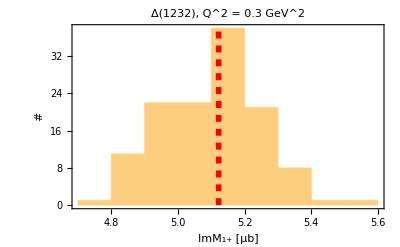
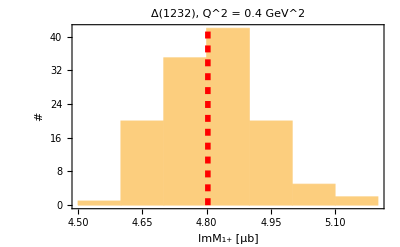
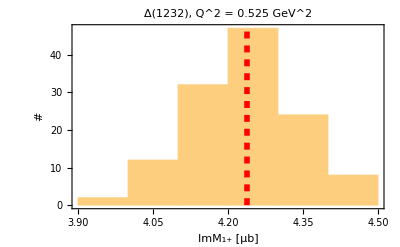
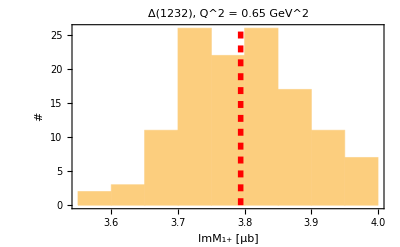
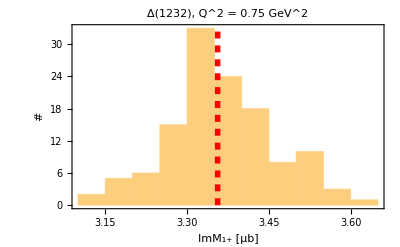
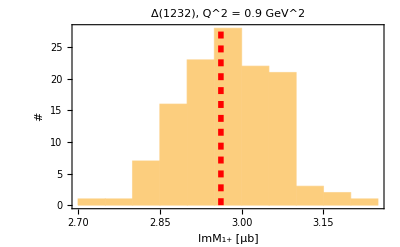
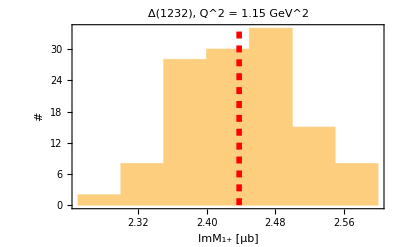
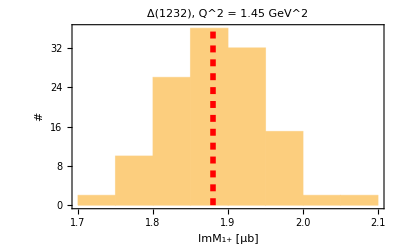

```mathematica
Table[ImMPlots[q],{q,1,NQ2BinsI}]
```

### Plot the bootstrap-distributions, for the 2nd resonance-region:

```mathematica
Do[N1440A12Plots[q]=Show[Histogram[Table[BootStrapN1440A12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"A_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1440, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1440A12[[1]][[q]],0},{BootStrapN1440A12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

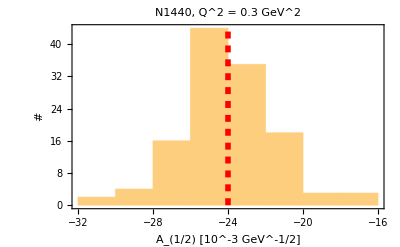
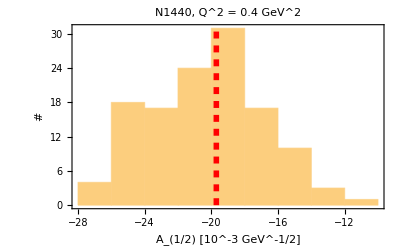
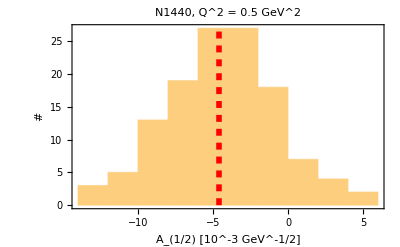
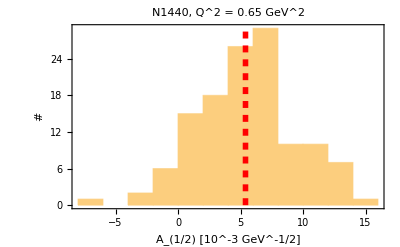
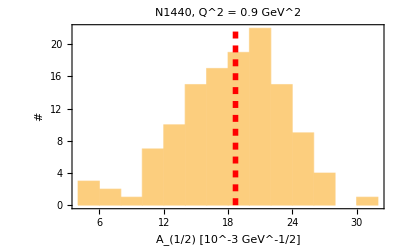
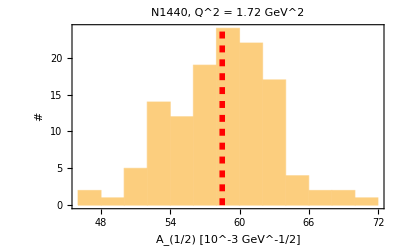
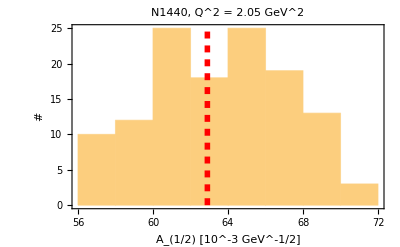
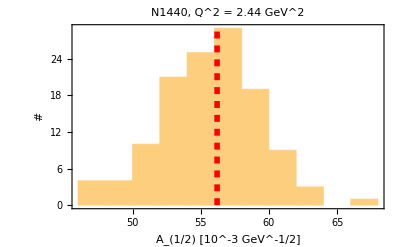

```mathematica
Table[N1440A12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1440S12Plots[q]=Show[Histogram[Table[BootStrapN1440S12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"S_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1440, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1440S12[[1]][[q]],0},{BootStrapN1440S12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

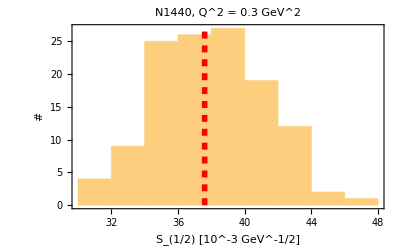
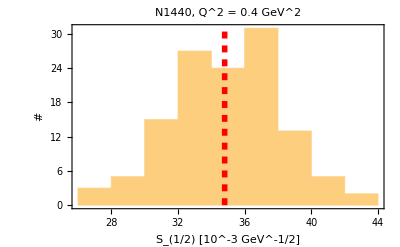
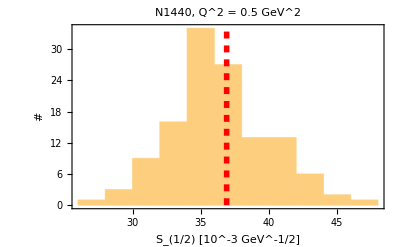
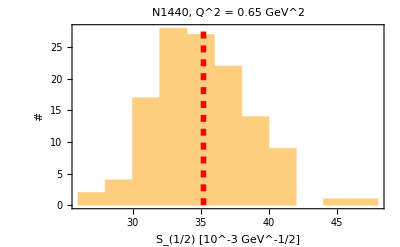
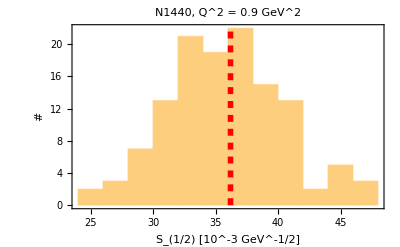
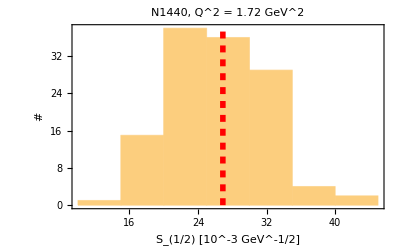
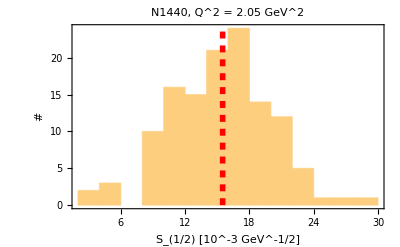
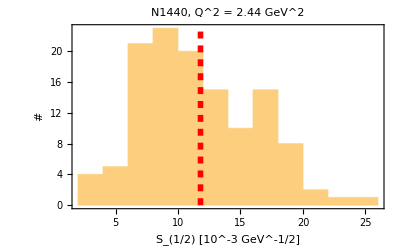

```mathematica
Table[N1440S12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1535A12Plots[q]=Show[Histogram[Table[BootStrapN1535A12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"A_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1535, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1535A12[[1]][[q]],0},{BootStrapN1535A12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

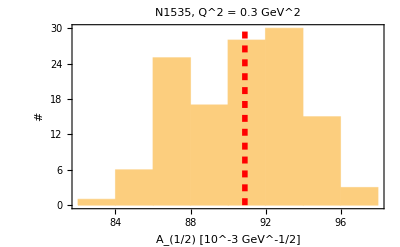
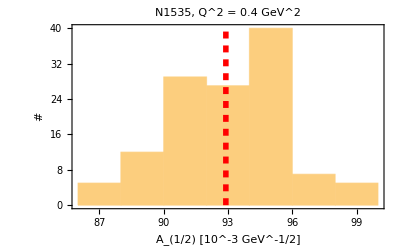
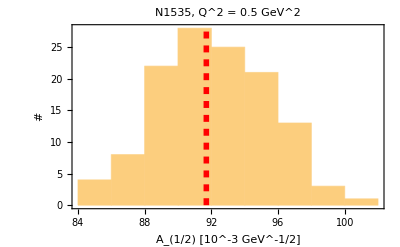
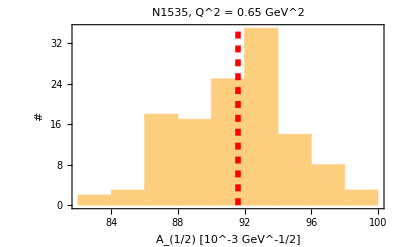
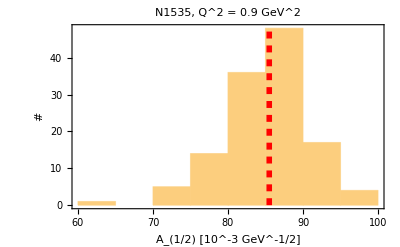
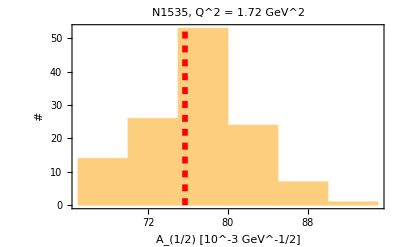
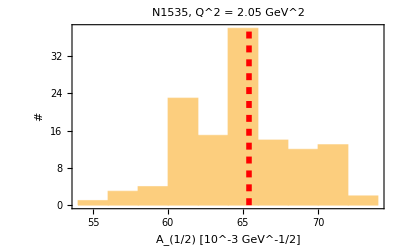
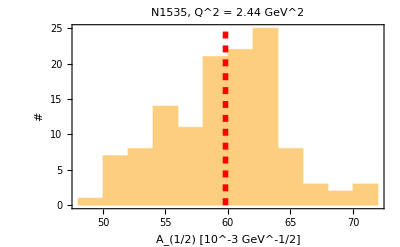

```mathematica
Table[N1535A12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1535S12Plots[q]=Show[Histogram[Table[BootStrapN1535S12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"S_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1535, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1535S12[[1]][[q]],0},{BootStrapN1535S12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

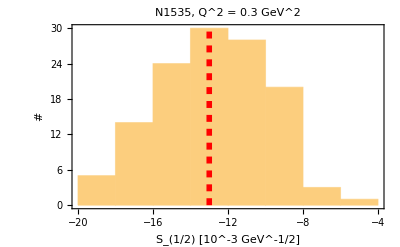
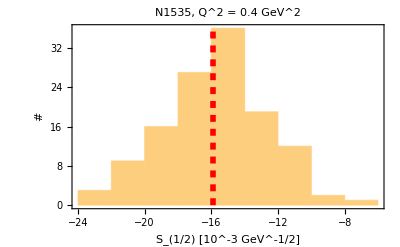
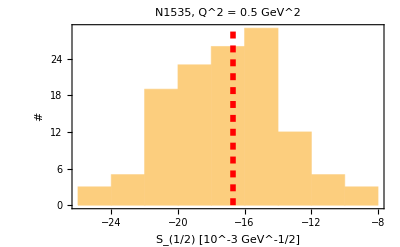
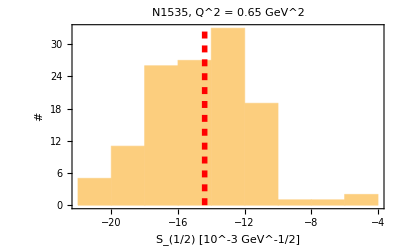
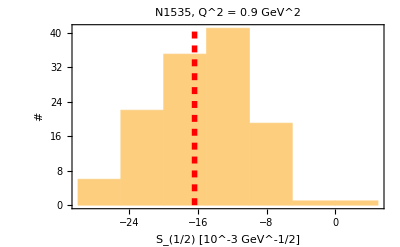
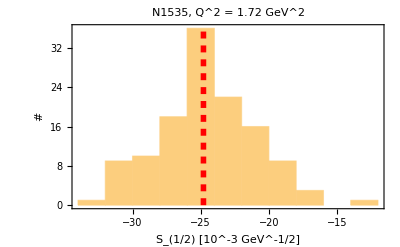
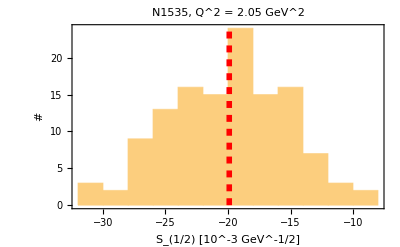
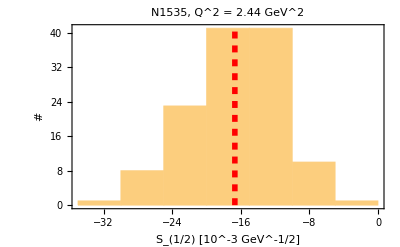

```mathematica
Table[N1535S12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1520A12Plots[q]=Show[Histogram[Table[BootStrapN1520A12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"A_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1520, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1520A12[[1]][[q]],0},{BootStrapN1520A12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

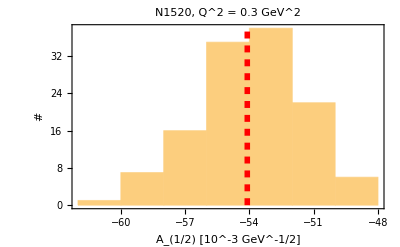
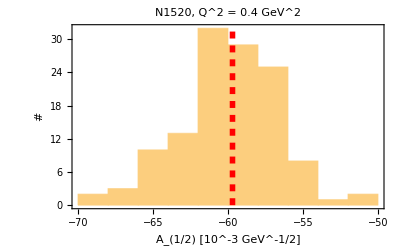
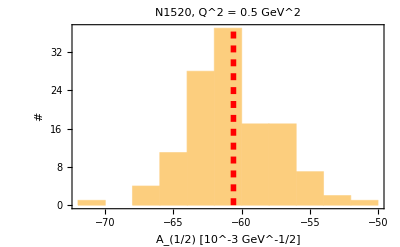
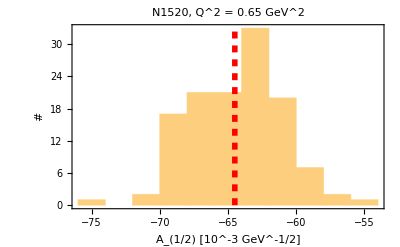
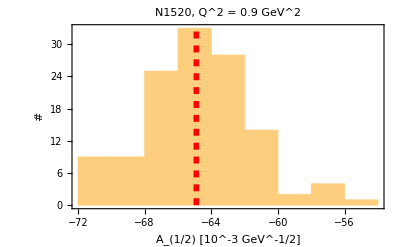
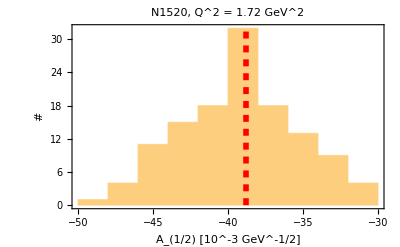
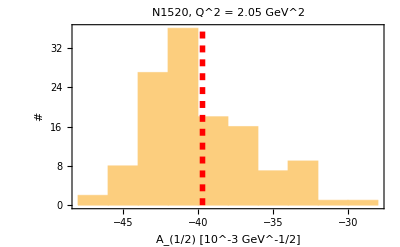
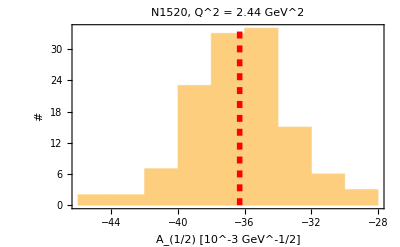

```mathematica
Table[N1520A12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1520S12Plots[q]=Show[Histogram[Table[BootStrapN1520S12[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"S_(1/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1520, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1520S12[[1]][[q]],0},{BootStrapN1520S12[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

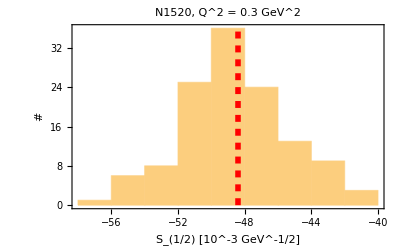
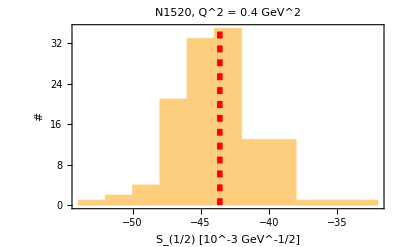
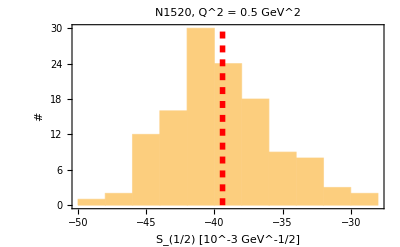
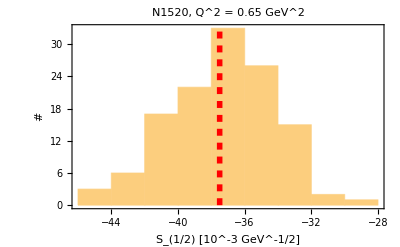
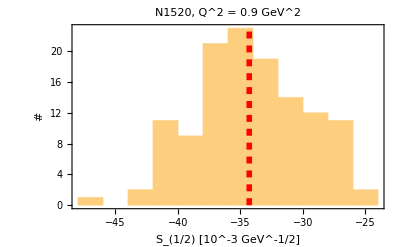
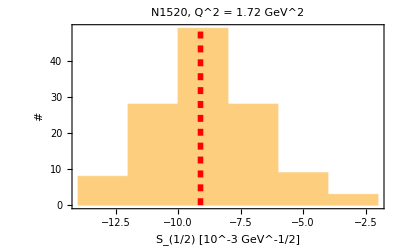
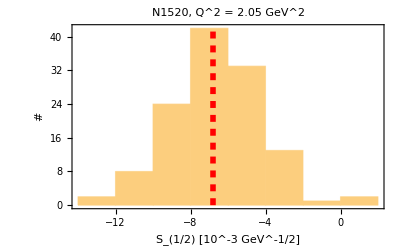
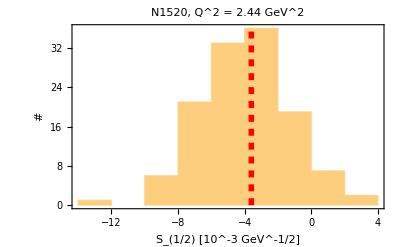

```mathematica
Table[N1520S12Plots[q],{q,1,NQ2Bins}]
```

```mathematica
Do[N1520A32Plots[q]=Show[Histogram[Table[BootStrapN1520A32[[n+1]][[q]],{n,1,NBoot}],Frame->True,Axes->False,FrameLabel->{"A_(3/2) [10^-3 GeV^-1/2]","#"},PlotLabel->"N1520, Q^2 = "<>ToString[Q2Values[[q]]]<>" GeV^2",PlotRange->All,Epilog->First@Graphics[{Red,Dashed,Thickness[0.01],Line[{{BootStrapN1520A32[[1]][[q]],0},{BootStrapN1520A32[[1]][[q]],300}}]}]]],{q,1,NQ2Bins}]
```

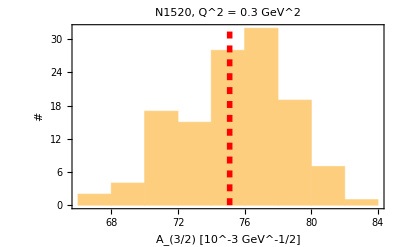
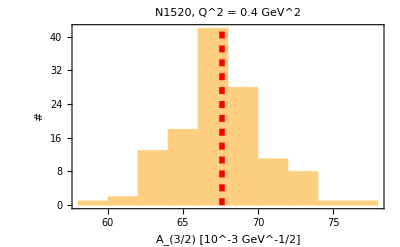
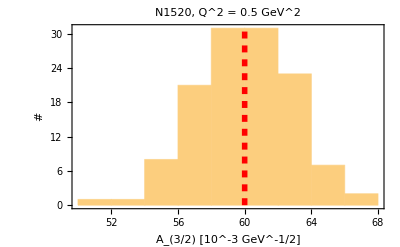
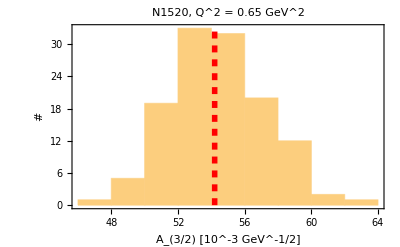
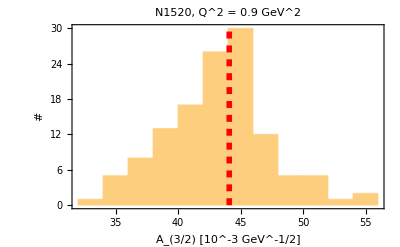
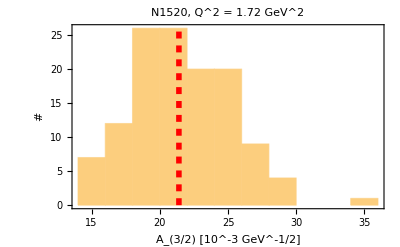
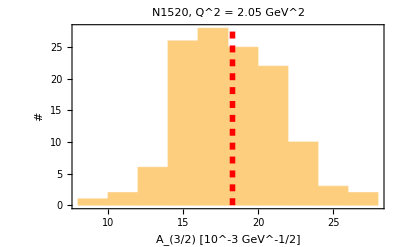
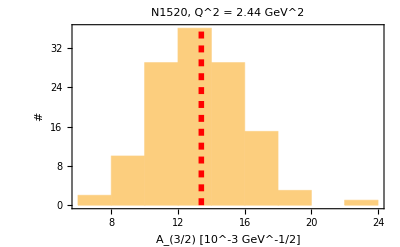

```mathematica
Table[N1520A32Plots[q],{q,1,NQ2Bins}]
```

### Interpolate the bootstrapped quantities for the Δ-resonance:

```mathematica
Do[IntBootImM[b]=Interpolation[Table[{Q2ValDeltaI[[i]],BootStrapImM[[b]][[i]]},{i,1,NQ2BinsI}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootREM[b]=Interpolation[Table[{Q2ValDeltaII[[i]],BootStrapREM[[b]][[i]]},{i,1,NQ2BinsII}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootRSM[b]=Interpolation[Table[{Q2ValDeltaII[[i]],BootStrapRSM[[b]][[i]]},{i,1,NQ2BinsII}]],{b,1,(NBoot+1)}]
```

### Interpolate the bootstrapped electrocouplings, for the 2nd resonance-region:

```mathematica
Do[IntBootN1440A12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1440A12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1440S12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1440S12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1535A12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1535A12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1535S12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1535S12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1520A12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1520A12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1520S12[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1520S12[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

```mathematica
Do[IntBootN1520A32[b]=Interpolation[Table[{Q2Values[[i]],BootStrapN1520A32[[b]][[i]]},{i,1,NQ2Bins}]],{b,1,(NBoot+1)}]
```

### Export the bootstrapped and interpolated electrocouplings and Δ-resonance parameters:

```mathematica
Q2Export={0.4,0.75,1.45,3.0,4.16}
NQ2Export=Dimensions[Q2Export][[1]]
```

{0.4,0.75,1.45,3.,4.16}

5

```mathematica
Export["ImM_Boot.dat",Table[Table[IntBootImM[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

ImM_Boot.dat

```mathematica
Export["REM_Boot.dat",Table[Table[IntBootREM[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

REM_Boot.dat

```mathematica
Export["RSM_Boot.dat",Table[Table[IntBootRSM[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

RSM_Boot.dat

```mathematica
Export["N1440A12Boot.dat",Table[Table[IntBootN1440A12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1440A12Boot.dat

```mathematica
Export["N1440S12Boot.dat",Table[Table[IntBootN1440S12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1440S12Boot.dat

```mathematica
Export["N1535A12Boot.dat",Table[Table[IntBootN1535A12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1535A12Boot.dat

```mathematica
Export["N1535S12Boot.dat",Table[Table[IntBootN1535S12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1535S12Boot.dat

```mathematica
Export["N1520A12Boot.dat",Table[Table[IntBootN1520A12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1520A12Boot.dat

```mathematica
Export["N1520S12Boot.dat",Table[Table[IntBootN1520S12[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1520S12Boot.dat

```mathematica
Export["N1520A32Boot.dat",Table[Table[IntBootN1520A32[b][Q2Export[[i]]],{i,1,NQ2Export}],{b,1,(NBoot+1)}]]
```

N1520A32Boot.dat

### Bootstrap the parameter ‘a = 0.71’, which appears in the parametrization of the form factors G_{ρ(ω)→πγ} (Q2):

```mathematica
aData=0.71
```

0.71

```mathematica
aPercentageError=20
```

20

```mathematica
aBootStrap=Table[If[b==1,aData,RandomVariate[NormalDistribution[aData,(aPercentageError/100.)*aData]]],{b,1,(NBoot+1)}];
```

```mathematica
Export["DipPar_Boot.dat",aBootStrap]
```

DipPar_Boot.dat